```mathematica
$Assumptions={Subscript[a, 0]>0};
```

```mathematica
ψ100=ResourceFunction["HydrogenWavefunction"][{1,0,0},Subscript[a, 0],{r,θ,ϕ}];
ψ210=ResourceFunction["HydrogenWavefunction"][{2,1,0},Subscript[a, 0],{r,θ,ϕ}];
```

```mathematica
InnerProd=Integrate[
Conjugate[#1]#2 r^2 Sin[θ]
,{r,0,∞},{θ,0,π},{ϕ,0,2π}]&;
```

```mathematica
Outer[InnerProd,{ψ100,ψ210},{ψ100,ψ210}]//MatrixForm (*Orthonormality*)
```

(1 | 0
0 | 1)

```mathematica
MatrixElement=Integrate[
Conjugate[#1] #2 #3 r^2 Sin[θ],
{r,0,∞},{θ,0,π},{ϕ,0,2π}]&;
```

```mathematica
MatrixElement[ψ210,r Cos[θ],ψ100]
```

(128 √2 a_0)/243

```mathematica
ψ211p=ResourceFunction["HydrogenWavefunction"][{2,1,+1},Subscript[a, 0],{r,θ,ϕ}];
ψ211m=ResourceFunction["HydrogenWavefunction"][{2,1,-1},Subscript[a, 0],{r,θ,ϕ}];
```

```mathematica
MatrixElement[ψ211p,r Cos[θ],ψ100]
MatrixElement[ψ211m,r Cos[θ],ψ100]
```

0

0

```mathematica
sol1=FullSimplify[DSolve[{-u''[x]- α^3 x u[x]== β u[x]},u[x],x],Assumptions->{α,β}∈Reals]
```

{{u[x]→AiryAi[-(x α^3+β)/((-α^3)^(2/3))] C[1]+AiryBi[-(x α^3+β)/((-α^3)^(2/3))] C[2]}}

```mathematica
Limit[AiryBi[x],x->Infinity]
```

∞

```mathematica
FullSimplify[DSolve[{-ψ''[x]- α x ψ [x]== β ψ[x]},ψ[x],x]]
```

```mathematica
FullSimplify[AiryAi[-β/(-α)^(2/3)] /.{β->(2m e)/ℏ^2,α->(2m e)/ℏ^2},Assumptions->m>0&&ℏ>0]
```

AiryAi[2^(1/3) (-(e m)/ℏ^2)^(1/3)]

```mathematica
thing=Solve[AiryAi[-β/(-α)^(2/3)] ==0,β][[1]]//Quiet
```

{β→-(-α)^(2/3) AiryAiZero[1]}

```mathematica
β==(β/.thing)//N
```

β==2.33811 (-1. α)^(2/3)

```mathematica
AiryAiZero[1]
```

AiryAiZero[1]

```mathematica
N[AiryAiZero[1]]
```

-2.33811

```mathematica
Solve[(2^(1/3) e)/(F0 (-ℏ^2/(F0 m))^(1/3))==x0,e]
```

```mathematica
{{e->(F0 x0 (-ℏ^2/(F0 m))^(1/3))/2^(1/3)}}//Simplify
```

{{e→(F0 x0 (-ℏ^2/(F0 m))^(1/3))/2^(1/3)}}

```mathematica
-(2 m e)/ℏ^2(-ℏ^2/(2m F0))^(2/3)//Simplify
```

(2^(1/3) e)/(F0 (-ℏ^2/(F0 m))^(1/3))

```mathematica
NSolve [x^3==-1]
```

{{x→-1.},{x→0.5-0.866025 ⅈ},{x→0.5+0.866025 ⅈ}}

```mathematica
AiryAiZero[1]//N
```

-2.33811

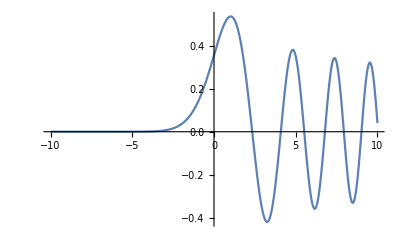

```mathematica
Plot[AiryAi[-x],{x,-10,10}]
```

```mathematica
N[(-1)^(1/3)]
```

0.5+0.866025 ⅈ

```mathematica
ψ=A x Exp[-α x];
Integrate[ψ^2,{x,0,Infinity}]
```

ConditionalExpression[A^2/(4 α^3), Re[α]>0]

```mathematica
(-ψ/A D[ψ/A,x,x]//Expand)
```

2 ⅇ^(-2 x α) x α-ⅇ^(-2 x α) x^2 α^2

```mathematica
T=Integrate[ψ(-ℏ^2/(2m)D[ψ,x,x]),{x,0,Infinity},Assumptions->α>0];
U=Integrate[ψ(F0 x)ψ,{x,0,Infinity},Assumptions->α>0];
H=(T+U)/.{A^2->4 α^3}
```

(3 F0)/(2 α)+(α^2 ℏ^2)/(2 m)

```mathematica
D[H,α]
```

-(3 F0)/(2 α^2)+(α ℏ^2)/m

```mathematica
H/.{α->((3m F0)/(2 ℏ^2))^(1/3)}//Simplify
```

(3 3^(2/3) F0)/(2 2^(2/3) ((F0 m)/ℏ^2)^(1/3))

```mathematica
(-AiryAiZero[1])/2^(1/3)
```

-AiryAiZero[1]/2^(1/3)

```mathematica
N[-AiryAiZero[1]/2^(1/3)]
```

1.85576

```mathematica
(3/2)^(5/3)//N
```

1.96556

```mathematica
ψ1=B x Exp[-α x^2/2];
Integrate[ψ1^2,{x,0,Infinity},Assumptions->α>0]
```

(B^2 √π)/(4 α^(3/2))

```mathematica
T=Integrate[ψ1(-ℏ^2/(2m)D[ψ1,x,x]),{x,0,Infinity},Assumptions->α>0]
U=Integrate[ψ1(F0 x)ψ1,{x,0,Infinity},Assumptions->α>0]
H=(T+U)/.{B^2->(4 α^(3/2))/(√π)}
```

(3 B^2 √π ℏ^2)/(16 m √α)

(B^2 F0)/(2 α^2)

(2 F0)/(√π √α)+(3 α ℏ^2)/(4 m)

```mathematica
D[H,α]
```

-F0/(√π α^(3/2))+(3 ℏ^2)/(4 m)

```mathematica
FullSimplify[H/.{α->((4m F0)/(3 ℏ^2 √π))^(2/3)},Assumptions->{m,F0,ℏ}∈Reals]//N
```

(1.86105 F0)/(((F0 m)/ℏ^2)^(1/3))

```mathematica
A=2A0 ϵ Cos[w/c k x-ω t];
-1/c D[A,t]
```

-(2 A0 ϵ ω Sin[(k w x)/c-t ω])/c